# Bistable networks: kinase with four states

## Finding the condition of multistationarity

Four different states for the Kinase

K1 + S -1> K1S -2> K1 + Sp     
K2 + S -3> K2S -4> K2 + Sp 
K1 -5> K2
K2S -6> K1S
K3 + S -7> K3S -8> K3 + Sp       
K2 -9> K3
K3S -10> K2S 
K4 + S -11> K4S -12> K4 + Sp     
K3 -13> K4
K4S -14> K3S
                                   
Sp-15>S  

Species
{S(1), Sp(2), K1 (3) ,K1S (4), K2(5), K2S(6), K3(7), K3S(8), K4(9), K4S(10) }

```mathematica
ClearAll["Global`*"];
A=Table[0,{15},{10}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[4]]=1;
A[[2]][[2]]=1;A[[2]][[3]]=1;A[[2]][[4]]=-1;
A[[3]][[1]]=-1;A[[3]][[5]]=-1;A[[3]][[6]]=1;
A[[4]][[2]]=1;A[[4]][[5]]=1;A[[4]][[6]]=-1;
A[[5]][[3]]=-1;A[[5]][[5]]=1;
A[[6]][[4]]=1;A[[6]][[6]]=-1;
A[[7]][[1]]=-1;A[[7]][[7]]=-1;A[[7]][[8]]=1;
A[[8]][[8]]=-1;A[[8]][[7]]=1;A[[8]][[2]]=1;
A[[9]][[5]]=-1;A[[9]][[7]]=1;
A[[10]][[8]]=-1;A[[10]][[6]]=1;
A[[11]][[1]]=-1;A[[11]][[9]]=-1;A[[11]][[10]]=1;
A[[12]][[10]]=-1;A[[12]][[9]]=1;A[[12]][[2]]=1;
A[[13]][[7]]=-1;A[[13]][[9]]=1;
A[[14]][[10]]=-1;A[[14]][[8]]=1;
A[[15]][[2]]=-1;A[[15]][[1]]=1;
stoiM=Transpose[A]
```

{{-1,0,-1,0,0,0,-1,0,0,0,-1,0,0,0,1},{0,1,0,1,0,0,0,1,0,0,0,1,0,0,-1},{-1,1,0,0,-1,0,0,0,0,0,0,0,0,0,0},{1,-1,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,-1,1,1,0,0,0,-1,0,0,0,0,0,0},{0,0,1,-1,0,-1,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,-1,1,1,0,0,0,-1,0,0},{0,0,0,0,0,0,1,-1,0,-1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,-1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,-1,0,-1,0}}

```mathematica
ks={Subscript[k, 1]*Subscript[x, 1]*Subscript[x, 3],Subscript[k, 2]*Subscript[x, 4],Subscript[k, 3]*Subscript[x, 1]*Subscript[x, 5],Subscript[k, 4]*Subscript[x, 6],Subscript[k, 5]*Subscript[x, 3],Subscript[k, 6]*Subscript[x, 6],Subscript[k, 7]*Subscript[x, 1]*Subscript[x, 7],Subscript[k, 8]*Subscript[x, 8],Subscript[k, 9]*Subscript[x, 5],Subscript[k, 10]*Subscript[x, 8],Subscript[k, 11]*Subscript[x, 1]*Subscript[x, 9],Subscript[k, 12]*Subscript[x, 10],Subscript[k, 13]*Subscript[x, 7],Subscript[k, 14]*Subscript[x, 10],Subscript[k, 15]*Subscript[x, 2]}
```

{k_1 x_1 x_3,k_2 x_4,k_3 x_1 x_5,k_4 x_6,k_5 x_3,k_6 x_6,k_7 x_1 x_7,k_8 x_8,k_9 x_5,k_10 x_8,k_11 x_1 x_9,k_12 x_10,k_13 x_7,k_14 x_10,k_15 x_2}

```mathematica
ssEqns=stoiM.ks
```

{k_15 x_2-k_1 x_1 x_3-k_3 x_1 x_5-k_7 x_1 x_7-k_11 x_1 x_9,-k_15 x_2+k_2 x_4+k_4 x_6+k_8 x_8+k_12 x_10,-k_5 x_3-k_1 x_1 x_3+k_2 x_4,k_1 x_1 x_3-k_2 x_4+k_6 x_6,k_5 x_3-k_9 x_5-k_3 x_1 x_5+k_4 x_6,k_3 x_1 x_5-k_4 x_6-k_6 x_6+k_10 x_8,k_9 x_5-k_13 x_7-k_7 x_1 x_7+k_8 x_8,k_7 x_1 x_7-k_8 x_8-k_10 x_8+k_14 x_10,k_13 x_7-k_11 x_1 x_9+k_12 x_10,k_11 x_1 x_9-k_12 x_10-k_14 x_10}

```mathematica
mC=RowReduce[NullSpace[A]]
```

{{1,1,0,1,0,1,0,1,0,1},{0,0,1,1,1,1,1,1,1,1}}

```mathematica
cons={Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 4]+Subscript[x, 6]+Subscript[x, 8]+Subscript[x, 10]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 7]+Subscript[x, 8]+Subscript[x, 9]+Subscript[x, 10]-Subscript[T, 2]}
```

{-T_1+x_1+x_2+x_4+x_6+x_8+x_10,-T_2+x_3+x_4+x_5+x_6+x_7+x_8+x_9+x_10}

```mathematica
sol1=Solve[Flatten[{cons[[2]],ssEqns[[2;;10]]}]==0,{Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[x, 10]}]
```

{{x_2→-((k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_10 k_11^2 k_14 T_2 x_1^2 (-k_13-k_7 x_1) ((-k_9 k_10 k_12 k_13+k_3 k_8 k_12 k_13 x_1+k_3 k_8 k_13 k_14 x_1+k_3 k_7 k_8 k_14 x_1^2)/(k_10 k_14 k_15 (k_13+k_7 x_1))-((-k_9-k_3 x_1) ((-k_4 k_5-k_5 k_6-k_1 k_6 x_1)/(k_5 k_15)-((-k_4-k_6) (-k_8/k_15-(k_8 k_12 k_13)/(k_14 k_15 (k_13+k_7 x_1))))/k_10))/(k_4+k_6)))/(-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))))),x_3→(k_2^2 k_6 (k_2 k_4 k_5+k_2 k_5 k_6) k_10 k_11^2 k_14 T_2 x_1^2 (k_9+k_3 x_1) (-k_13-k_7 x_1))/((k_4+k_6) (-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))))),x_4→(k_2 k_6 (k_2 k_4 k_5+k_2 k_5 k_6) k_10 k_11^2 k_14 T_2 x_1^2 (k_5+k_1 x_1) (k_9+k_3 x_1) (-k_13-k_7 x_1))/((k_4+k_6) (-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))))),x_5→(k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_10 k_11^2 k_14 T_2 x_1^2 (-k_13-k_7 x_1))/(-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))),x_6→-((k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_10 k_11^2 k_14 T_2 x_1^2 (-k_9-k_3 x_1) (-k_13-k_7 x_1))/((k_4+k_6) (-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))))),x_7→(k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_9 (k_8+k_10) k_11^2 k_14 T_2 x_1^2 (-k_13-k_7 x_1))/((k_13+k_7 x_1) (-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))))),x_8→(k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_9 k_11^2 k_14 T_2 x_1^2 (-k_13-k_7 x_1))/(-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))),x_9→-((k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_11 (-k_8 k_9 k_12 k_13-k_9 k_10 k_12 k_13-k_8 k_9 k_13 k_14-k_9 k_10 k_13 k_14) T_2 x_1 (-k_13-k_7 x_1))/((k_13+k_7 x_1) (-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))))),x_10→(k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_9 (k_8+k_10) k_11^2 k_13 T_2 x_1^2 (-k_13-k_7 x_1))/((k_13+k_7 x_1) (-k_2 k_5 (-k_9-k_3 x_1) (k_10 k_11 k_14 x_1 (-k_13-k_7 x_1) (k_2 k_5 (k_2 k_11 x_1+k_6 k_11 x_1)+k_2 k_6 (k_2 k_11 x_1+k_1 k_11 x_1^2))-(-k_4-k_6) (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))+(k_2 k_4 k_5+k_2 k_5 k_6) (-k_3 x_1 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_8 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1)))+k_10 (k_2^2 k_5 k_11^2 k_14 x_1^2 (-k_13-k_7 x_1)-k_9 (k_2 k_5 k_11 k_13 x_1 (k_2 k_12+k_2 k_11 x_1)+k_2 k_5 k_11 k_14 x_1 (k_2 k_13+k_2 k_11 x_1))))))}}

```mathematica
term=Simplify[cons[[1]]/.sol1[[1]]]
```

(-k_6 k_10 k_11 k_14 k_15 (T_1-T_2-x_1) x_1 (k_5+k_1 x_1) (k_9+k_3 x_1) (k_13+k_7 x_1)+k_2 (k_6 k_10 k_11 k_14 x_1 (k_9+k_3 x_1) (k_13+k_7 x_1) (k_1 T_2 x_1+k_15 (-T_1+x_1))+k_4 k_5 (k_10 k_11 k_14 x_1 (k_13+k_7 x_1) (k_3 T_2 x_1+k_15 (-T_1+x_1))+k_8 k_9 (k_11 k_14 x_1 (k_7 T_2 x_1+k_15 (-T_1+x_1))+k_12 k_13 (k_11 T_2 x_1+k_15 (-T_1+x_1))+k_13 (k_11 k_15 x_1 (-T_1+T_2+x_1)+k_14 (k_11 T_2 x_1+k_15 (-T_1+x_1))))+k_9 (-k_11 k_14 k_15 (T_1-T_2-x_1) x_1 (k_13+k_7 x_1)+k_10 (k_11 k_14 x_1 (k_7 T_2 x_1+k_15 (-T_1+x_1))+k_12 k_13 (k_11 T_2 x_1+k_15 (-T_1+x_1))+k_13 (k_11 k_15 x_1 (-T_1+T_2+x_1)+k_14 (k_11 T_2 x_1+k_15 (-T_1+x_1))))))+k_5 (-k_10 k_11 k_14 k_15 (T_1-T_2-x_1) x_1 (k_9+k_3 x_1) (k_13+k_7 x_1)+k_6 (k_10 k_11 k_14 x_1 (k_13+k_7 x_1) (k_3 T_2 x_1+k_15 (-T_1+x_1))+k_8 k_9 (k_11 k_14 x_1 (k_7 T_2 x_1+k_15 (-T_1+x_1))+k_12 k_13 (k_11 T_2 x_1+k_15 (-T_1+x_1))+k_13 (k_11 k_15 x_1 (-T_1+T_2+x_1)+k_14 (k_11 T_2 x_1+k_15 (-T_1+x_1))))+k_9 (-k_11 k_14 k_15 (T_1-T_2-x_1) x_1 (k_13+k_7 x_1)+k_10 (k_11 k_14 x_1 (k_7 T_2 x_1+k_15 (-T_1+x_1))+k_12 k_13 (k_11 T_2 x_1+k_15 (-T_1+x_1))+k_13 (k_11 k_15 x_1 (-T_1+T_2+x_1)+k_14 (k_11 T_2 x_1+k_15 (-T_1+x_1)))))))))/(k_15 (k_6 k_10 k_11 k_14 x_1 (k_5+k_1 x_1) (k_9+k_3 x_1) (k_13+k_7 x_1)+k_2 (k_6 k_10 k_11 k_14 x_1 (k_9+k_3 x_1) (k_13+k_7 x_1)+k_4 k_5 (k_10 k_11 k_14 x_1 (k_13+k_7 x_1)+k_8 k_9 (k_12 k_13+k_11 k_14 x_1+k_13 (k_14+k_11 x_1))+k_9 (k_11 k_14 x_1 (k_13+k_7 x_1)+k_10 (k_12 k_13+k_11 k_14 x_1+k_13 (k_14+k_11 x_1))))+k_5 (k_10 k_11 k_14 x_1 (k_9+k_3 x_1) (k_13+k_7 x_1)+k_6 (k_10 k_11 k_14 x_1 (k_13+k_7 x_1)+k_8 k_9 (k_12 k_13+k_11 k_14 x_1+k_13 (k_14+k_11 x_1))+k_9 (k_11 k_14 x_1 (k_13+k_7 x_1)+k_10 (k_12 k_13+k_11 k_14 x_1+k_13 (k_14+k_11 x_1))))))))

```mathematica
Together[term]
```

(-k_2 k_4 k_5 k_8 k_9 k_12 k_13 k_15 T_1-k_2 k_5 k_6 k_8 k_9 k_12 k_13 k_15 T_1-k_2 k_4 k_5 k_9 k_10 k_12 k_13 k_15 T_1-k_2 k_5 k_6 k_9 k_10 k_12 k_13 k_15 T_1-k_2 k_4 k_5 k_8 k_9 k_13 k_14 k_15 T_1-k_2 k_5 k_6 k_8 k_9 k_13 k_14 k_15 T_1-k_2 k_4 k_5 k_9 k_10 k_13 k_14 k_15 T_1-k_2 k_5 k_6 k_9 k_10 k_13 k_14 k_15 T_1+k_2 k_4 k_5 k_8 k_9 k_12 k_13 k_15 x_1+k_2 k_5 k_6 k_8 k_9 k_12 k_13 k_15 x_1+k_2 k_4 k_5 k_9 k_10 k_12 k_13 k_15 x_1+k_2 k_5 k_6 k_9 k_10 k_12 k_13 k_15 x_1+k_2 k_4 k_5 k_8 k_9 k_13 k_14 k_15 x_1+k_2 k_5 k_6 k_8 k_9 k_13 k_14 k_15 x_1+k_2 k_4 k_5 k_9 k_10 k_13 k_14 k_15 x_1+k_2 k_5 k_6 k_9 k_10 k_13 k_14 k_15 x_1-k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_15 T_1 x_1-k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_15 T_1 x_1-k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_15 T_1 x_1-k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_15 T_1 x_1-k_2 k_4 k_5 k_8 k_9 k_11 k_14 k_15 T_1 x_1-k_2 k_5 k_6 k_8 k_9 k_11 k_14 k_15 T_1 x_1-k_2 k_4 k_5 k_9 k_10 k_11 k_14 k_15 T_1 x_1-k_2 k_5 k_6 k_9 k_10 k_11 k_14 k_15 T_1 x_1-k_2 k_4 k_5 k_9 k_11 k_13 k_14 k_15 T_1 x_1-k_2 k_5 k_6 k_9 k_11 k_13 k_14 k_15 T_1 x_1-k_2 k_4 k_5 k_10 k_11 k_13 k_14 k_15 T_1 x_1-k_2 k_5 k_6 k_10 k_11 k_13 k_14 k_15 T_1 x_1-k_2 k_5 k_9 k_10 k_11 k_13 k_14 k_15 T_1 x_1-k_2 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_1 x_1-k_5 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_1 x_1+k_2 k_4 k_5 k_8 k_9 k_11 k_12 k_13 T_2 x_1+k_2 k_5 k_6 k_8 k_9 k_11 k_12 k_13 T_2 x_1+k_2 k_4 k_5 k_9 k_10 k_11 k_12 k_13 T_2 x_1+k_2 k_5 k_6 k_9 k_10 k_11 k_12 k_13 T_2 x_1+k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_14 T_2 x_1+k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_14 T_2 x_1+k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_14 T_2 x_1+k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_14 T_2 x_1+k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_15 T_2 x_1+k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_15 T_2 x_1+k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_15 T_2 x_1+k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_15 T_2 x_1+k_2 k_4 k_5 k_9 k_11 k_13 k_14 k_15 T_2 x_1+k_2 k_5 k_6 k_9 k_11 k_13 k_14 k_15 T_2 x_1+k_2 k_5 k_9 k_10 k_11 k_13 k_14 k_15 T_2 x_1+k_5 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_2 x_1+k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_15 x_1^2+k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_15 x_1^2+k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_15 x_1^2+k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_15 x_1^2+k_2 k_4 k_5 k_8 k_9 k_11 k_14 k_15 x_1^2+k_2 k_5 k_6 k_8 k_9 k_11 k_14 k_15 x_1^2+k_2 k_4 k_5 k_9 k_10 k_11 k_14 k_15 x_1^2+k_2 k_5 k_6 k_9 k_10 k_11 k_14 k_15 x_1^2+k_2 k_4 k_5 k_9 k_11 k_13 k_14 k_15 x_1^2+k_2 k_5 k_6 k_9 k_11 k_13 k_14 k_15 x_1^2+k_2 k_4 k_5 k_10 k_11 k_13 k_14 k_15 x_1^2+k_2 k_5 k_6 k_10 k_11 k_13 k_14 k_15 x_1^2+k_2 k_5 k_9 k_10 k_11 k_13 k_14 k_15 x_1^2+k_2 k_6 k_9 k_10 k_11 k_13 k_14 k_15 x_1^2+k_5 k_6 k_9 k_10 k_11 k_13 k_14 k_15 x_1^2-k_2 k_4 k_5 k_7 k_9 k_11 k_14 k_15 T_1 x_1^2-k_2 k_5 k_6 k_7 k_9 k_11 k_14 k_15 T_1 x_1^2-k_2 k_4 k_5 k_7 k_10 k_11 k_14 k_15 T_1 x_1^2-k_2 k_5 k_6 k_7 k_10 k_11 k_14 k_15 T_1 x_1^2-k_2 k_5 k_7 k_9 k_10 k_11 k_14 k_15 T_1 x_1^2-k_2 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_1 x_1^2-k_5 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_1 x_1^2-k_2 k_3 k_5 k_10 k_11 k_13 k_14 k_15 T_1 x_1^2-k_2 k_3 k_6 k_10 k_11 k_13 k_14 k_15 T_1 x_1^2-k_3 k_5 k_6 k_10 k_11 k_13 k_14 k_15 T_1 x_1^2-k_1 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_1 x_1^2+k_2 k_4 k_5 k_7 k_8 k_9 k_11 k_14 T_2 x_1^2+k_2 k_5 k_6 k_7 k_8 k_9 k_11 k_14 T_2 x_1^2+k_2 k_4 k_5 k_7 k_9 k_10 k_11 k_14 T_2 x_1^2+k_2 k_5 k_6 k_7 k_9 k_10 k_11 k_14 T_2 x_1^2+k_2 k_3 k_4 k_5 k_10 k_11 k_13 k_14 T_2 x_1^2+k_2 k_3 k_5 k_6 k_10 k_11 k_13 k_14 T_2 x_1^2+k_1 k_2 k_6 k_9 k_10 k_11 k_13 k_14 T_2 x_1^2+k_2 k_4 k_5 k_7 k_9 k_11 k_14 k_15 T_2 x_1^2+k_2 k_5 k_6 k_7 k_9 k_11 k_14 k_15 T_2 x_1^2+k_2 k_5 k_7 k_9 k_10 k_11 k_14 k_15 T_2 x_1^2+k_5 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_2 x_1^2+k_2 k_3 k_5 k_10 k_11 k_13 k_14 k_15 T_2 x_1^2+k_3 k_5 k_6 k_10 k_11 k_13 k_14 k_15 T_2 x_1^2+k_1 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_2 x_1^2+k_2 k_4 k_5 k_7 k_9 k_11 k_14 k_15 x_1^3+k_2 k_5 k_6 k_7 k_9 k_11 k_14 k_15 x_1^3+k_2 k_4 k_5 k_7 k_10 k_11 k_14 k_15 x_1^3+k_2 k_5 k_6 k_7 k_10 k_11 k_14 k_15 x_1^3+k_2 k_5 k_7 k_9 k_10 k_11 k_14 k_15 x_1^3+k_2 k_6 k_7 k_9 k_10 k_11 k_14 k_15 x_1^3+k_5 k_6 k_7 k_9 k_10 k_11 k_14 k_15 x_1^3+k_2 k_3 k_5 k_10 k_11 k_13 k_14 k_15 x_1^3+k_2 k_3 k_6 k_10 k_11 k_13 k_14 k_15 x_1^3+k_3 k_5 k_6 k_10 k_11 k_13 k_14 k_15 x_1^3+k_1 k_6 k_9 k_10 k_11 k_13 k_14 k_15 x_1^3-k_2 k_3 k_5 k_7 k_10 k_11 k_14 k_15 T_1 x_1^3-k_2 k_3 k_6 k_7 k_10 k_11 k_14 k_15 T_1 x_1^3-k_3 k_5 k_6 k_7 k_10 k_11 k_14 k_15 T_1 x_1^3-k_1 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_1 x_1^3-k_1 k_3 k_6 k_10 k_11 k_13 k_14 k_15 T_1 x_1^3+k_2 k_3 k_4 k_5 k_7 k_10 k_11 k_14 T_2 x_1^3+k_2 k_3 k_5 k_6 k_7 k_10 k_11 k_14 T_2 x_1^3+k_1 k_2 k_6 k_7 k_9 k_10 k_11 k_14 T_2 x_1^3+k_1 k_2 k_3 k_6 k_10 k_11 k_13 k_14 T_2 x_1^3+k_2 k_3 k_5 k_7 k_10 k_11 k_14 k_15 T_2 x_1^3+k_3 k_5 k_6 k_7 k_10 k_11 k_14 k_15 T_2 x_1^3+k_1 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_2 x_1^3+k_1 k_3 k_6 k_10 k_11 k_13 k_14 k_15 T_2 x_1^3+k_2 k_3 k_5 k_7 k_10 k_11 k_14 k_15 x_1^4+k_2 k_3 k_6 k_7 k_10 k_11 k_14 k_15 x_1^4+k_3 k_5 k_6 k_7 k_10 k_11 k_14 k_15 x_1^4+k_1 k_6 k_7 k_9 k_10 k_11 k_14 k_15 x_1^4+k_1 k_3 k_6 k_10 k_11 k_13 k_14 k_15 x_1^4-k_1 k_3 k_6 k_7 k_10 k_11 k_14 k_15 T_1 x_1^4+k_1 k_2 k_3 k_6 k_7 k_10 k_11 k_14 T_2 x_1^4+k_1 k_3 k_6 k_7 k_10 k_11 k_14 k_15 T_2 x_1^4+k_1 k_3 k_6 k_7 k_10 k_11 k_14 k_15 x_1^5)/(k_15 (k_2 k_4 k_5 k_8 k_9 k_12 k_13+k_2 k_5 k_6 k_8 k_9 k_12 k_13+k_2 k_4 k_5 k_9 k_10 k_12 k_13+k_2 k_5 k_6 k_9 k_10 k_12 k_13+k_2 k_4 k_5 k_8 k_9 k_13 k_14+k_2 k_5 k_6 k_8 k_9 k_13 k_14+k_2 k_4 k_5 k_9 k_10 k_13 k_14+k_2 k_5 k_6 k_9 k_10 k_13 k_14+k_2 k_4 k_5 k_8 k_9 k_11 k_13 x_1+k_2 k_5 k_6 k_8 k_9 k_11 k_13 x_1+k_2 k_4 k_5 k_9 k_10 k_11 k_13 x_1+k_2 k_5 k_6 k_9 k_10 k_11 k_13 x_1+k_2 k_4 k_5 k_8 k_9 k_11 k_14 x_1+k_2 k_5 k_6 k_8 k_9 k_11 k_14 x_1+k_2 k_4 k_5 k_9 k_10 k_11 k_14 x_1+k_2 k_5 k_6 k_9 k_10 k_11 k_14 x_1+k_2 k_4 k_5 k_9 k_11 k_13 k_14 x_1+k_2 k_5 k_6 k_9 k_11 k_13 k_14 x_1+k_2 k_4 k_5 k_10 k_11 k_13 k_14 x_1+k_2 k_5 k_6 k_10 k_11 k_13 k_14 x_1+k_2 k_5 k_9 k_10 k_11 k_13 k_14 x_1+k_2 k_6 k_9 k_10 k_11 k_13 k_14 x_1+k_5 k_6 k_9 k_10 k_11 k_13 k_14 x_1+k_2 k_4 k_5 k_7 k_9 k_11 k_14 x_1^2+k_2 k_5 k_6 k_7 k_9 k_11 k_14 x_1^2+k_2 k_4 k_5 k_7 k_10 k_11 k_14 x_1^2+k_2 k_5 k_6 k_7 k_10 k_11 k_14 x_1^2+k_2 k_5 k_7 k_9 k_10 k_11 k_14 x_1^2+k_2 k_6 k_7 k_9 k_10 k_11 k_14 x_1^2+k_5 k_6 k_7 k_9 k_10 k_11 k_14 x_1^2+k_2 k_3 k_5 k_10 k_11 k_13 k_14 x_1^2+k_2 k_3 k_6 k_10 k_11 k_13 k_14 x_1^2+k_3 k_5 k_6 k_10 k_11 k_13 k_14 x_1^2+k_1 k_6 k_9 k_10 k_11 k_13 k_14 x_1^2+k_2 k_3 k_5 k_7 k_10 k_11 k_14 x_1^3+k_2 k_3 k_6 k_7 k_10 k_11 k_14 x_1^3+k_3 k_5 k_6 k_7 k_10 k_11 k_14 x_1^3+k_1 k_6 k_7 k_9 k_10 k_11 k_14 x_1^3+k_1 k_3 k_6 k_10 k_11 k_13 k_14 x_1^3+k_1 k_3 k_6 k_7 k_10 k_11 k_14 x_1^4))

```mathematica
polynomial=Collect[Numerator[Together[term]],Subscript[x, 1]]
```

-k_2 k_4 k_5 k_8 k_9 k_12 k_13 k_15 T_1-k_2 k_5 k_6 k_8 k_9 k_12 k_13 k_15 T_1-k_2 k_4 k_5 k_9 k_10 k_12 k_13 k_15 T_1-k_2 k_5 k_6 k_9 k_10 k_12 k_13 k_15 T_1-k_2 k_4 k_5 k_8 k_9 k_13 k_14 k_15 T_1-k_2 k_5 k_6 k_8 k_9 k_13 k_14 k_15 T_1-k_2 k_4 k_5 k_9 k_10 k_13 k_14 k_15 T_1-k_2 k_5 k_6 k_9 k_10 k_13 k_14 k_15 T_1+(k_2 k_4 k_5 k_8 k_9 k_12 k_13 k_15+k_2 k_5 k_6 k_8 k_9 k_12 k_13 k_15+k_2 k_4 k_5 k_9 k_10 k_12 k_13 k_15+k_2 k_5 k_6 k_9 k_10 k_12 k_13 k_15+k_2 k_4 k_5 k_8 k_9 k_13 k_14 k_15+k_2 k_5 k_6 k_8 k_9 k_13 k_14 k_15+k_2 k_4 k_5 k_9 k_10 k_13 k_14 k_15+k_2 k_5 k_6 k_9 k_10 k_13 k_14 k_15-k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_15 T_1-k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_15 T_1-k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_15 T_1-k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_15 T_1-k_2 k_4 k_5 k_8 k_9 k_11 k_14 k_15 T_1-k_2 k_5 k_6 k_8 k_9 k_11 k_14 k_15 T_1-k_2 k_4 k_5 k_9 k_10 k_11 k_14 k_15 T_1-k_2 k_5 k_6 k_9 k_10 k_11 k_14 k_15 T_1-k_2 k_4 k_5 k_9 k_11 k_13 k_14 k_15 T_1-k_2 k_5 k_6 k_9 k_11 k_13 k_14 k_15 T_1-k_2 k_4 k_5 k_10 k_11 k_13 k_14 k_15 T_1-k_2 k_5 k_6 k_10 k_11 k_13 k_14 k_15 T_1-k_2 k_5 k_9 k_10 k_11 k_13 k_14 k_15 T_1-k_2 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_1-k_5 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_1+k_2 k_4 k_5 k_8 k_9 k_11 k_12 k_13 T_2+k_2 k_5 k_6 k_8 k_9 k_11 k_12 k_13 T_2+k_2 k_4 k_5 k_9 k_10 k_11 k_12 k_13 T_2+k_2 k_5 k_6 k_9 k_10 k_11 k_12 k_13 T_2+k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_14 T_2+k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_14 T_2+k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_14 T_2+k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_14 T_2+k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_15 T_2+k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_15 T_2+k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_15 T_2+k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_15 T_2+k_2 k_4 k_5 k_9 k_11 k_13 k_14 k_15 T_2+k_2 k_5 k_6 k_9 k_11 k_13 k_14 k_15 T_2+k_2 k_5 k_9 k_10 k_11 k_13 k_14 k_15 T_2+k_5 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_2) x_1+(k_2 k_4 k_5 k_8 k_9 k_11 k_13 k_15+k_2 k_5 k_6 k_8 k_9 k_11 k_13 k_15+k_2 k_4 k_5 k_9 k_10 k_11 k_13 k_15+k_2 k_5 k_6 k_9 k_10 k_11 k_13 k_15+k_2 k_4 k_5 k_8 k_9 k_11 k_14 k_15+k_2 k_5 k_6 k_8 k_9 k_11 k_14 k_15+k_2 k_4 k_5 k_9 k_10 k_11 k_14 k_15+k_2 k_5 k_6 k_9 k_10 k_11 k_14 k_15+k_2 k_4 k_5 k_9 k_11 k_13 k_14 k_15+k_2 k_5 k_6 k_9 k_11 k_13 k_14 k_15+k_2 k_4 k_5 k_10 k_11 k_13 k_14 k_15+k_2 k_5 k_6 k_10 k_11 k_13 k_14 k_15+k_2 k_5 k_9 k_10 k_11 k_13 k_14 k_15+k_2 k_6 k_9 k_10 k_11 k_13 k_14 k_15+k_5 k_6 k_9 k_10 k_11 k_13 k_14 k_15-k_2 k_4 k_5 k_7 k_9 k_11 k_14 k_15 T_1-k_2 k_5 k_6 k_7 k_9 k_11 k_14 k_15 T_1-k_2 k_4 k_5 k_7 k_10 k_11 k_14 k_15 T_1-k_2 k_5 k_6 k_7 k_10 k_11 k_14 k_15 T_1-k_2 k_5 k_7 k_9 k_10 k_11 k_14 k_15 T_1-k_2 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_1-k_5 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_1-k_2 k_3 k_5 k_10 k_11 k_13 k_14 k_15 T_1-k_2 k_3 k_6 k_10 k_11 k_13 k_14 k_15 T_1-k_3 k_5 k_6 k_10 k_11 k_13 k_14 k_15 T_1-k_1 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_1+k_2 k_4 k_5 k_7 k_8 k_9 k_11 k_14 T_2+k_2 k_5 k_6 k_7 k_8 k_9 k_11 k_14 T_2+k_2 k_4 k_5 k_7 k_9 k_10 k_11 k_14 T_2+k_2 k_5 k_6 k_7 k_9 k_10 k_11 k_14 T_2+k_2 k_3 k_4 k_5 k_10 k_11 k_13 k_14 T_2+k_2 k_3 k_5 k_6 k_10 k_11 k_13 k_14 T_2+k_1 k_2 k_6 k_9 k_10 k_11 k_13 k_14 T_2+k_2 k_4 k_5 k_7 k_9 k_11 k_14 k_15 T_2+k_2 k_5 k_6 k_7 k_9 k_11 k_14 k_15 T_2+k_2 k_5 k_7 k_9 k_10 k_11 k_14 k_15 T_2+k_5 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_2+k_2 k_3 k_5 k_10 k_11 k_13 k_14 k_15 T_2+k_3 k_5 k_6 k_10 k_11 k_13 k_14 k_15 T_2+k_1 k_6 k_9 k_10 k_11 k_13 k_14 k_15 T_2) x_1^2+(k_2 k_4 k_5 k_7 k_9 k_11 k_14 k_15+k_2 k_5 k_6 k_7 k_9 k_11 k_14 k_15+k_2 k_4 k_5 k_7 k_10 k_11 k_14 k_15+k_2 k_5 k_6 k_7 k_10 k_11 k_14 k_15+k_2 k_5 k_7 k_9 k_10 k_11 k_14 k_15+k_2 k_6 k_7 k_9 k_10 k_11 k_14 k_15+k_5 k_6 k_7 k_9 k_10 k_11 k_14 k_15+k_2 k_3 k_5 k_10 k_11 k_13 k_14 k_15+k_2 k_3 k_6 k_10 k_11 k_13 k_14 k_15+k_3 k_5 k_6 k_10 k_11 k_13 k_14 k_15+k_1 k_6 k_9 k_10 k_11 k_13 k_14 k_15-k_2 k_3 k_5 k_7 k_10 k_11 k_14 k_15 T_1-k_2 k_3 k_6 k_7 k_10 k_11 k_14 k_15 T_1-k_3 k_5 k_6 k_7 k_10 k_11 k_14 k_15 T_1-k_1 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_1-k_1 k_3 k_6 k_10 k_11 k_13 k_14 k_15 T_1+k_2 k_3 k_4 k_5 k_7 k_10 k_11 k_14 T_2+k_2 k_3 k_5 k_6 k_7 k_10 k_11 k_14 T_2+k_1 k_2 k_6 k_7 k_9 k_10 k_11 k_14 T_2+k_1 k_2 k_3 k_6 k_10 k_11 k_13 k_14 T_2+k_2 k_3 k_5 k_7 k_10 k_11 k_14 k_15 T_2+k_3 k_5 k_6 k_7 k_10 k_11 k_14 k_15 T_2+k_1 k_6 k_7 k_9 k_10 k_11 k_14 k_15 T_2+k_1 k_3 k_6 k_10 k_11 k_13 k_14 k_15 T_2) x_1^3+(k_2 k_3 k_5 k_7 k_10 k_11 k_14 k_15+k_2 k_3 k_6 k_7 k_10 k_11 k_14 k_15+k_3 k_5 k_6 k_7 k_10 k_11 k_14 k_15+k_1 k_6 k_7 k_9 k_10 k_11 k_14 k_15+k_1 k_3 k_6 k_10 k_11 k_13 k_14 k_15-k_1 k_3 k_6 k_7 k_10 k_11 k_14 k_15 T_1+k_1 k_2 k_3 k_6 k_7 k_10 k_11 k_14 T_2+k_1 k_3 k_6 k_7 k_10 k_11 k_14 k_15 T_2) x_1^4+k_1 k_3 k_6 k_7 k_10 k_11 k_14 k_15 x_1^5

#### Sampling

```mathematica
ClearAll["Global`*"];
pol=-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 12] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]) Subscript[x, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]) Subscript[x, 1]^2+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 1] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]) Subscript[x, 1]^3+(Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[k, 14] Subscript[k, 15]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[T, 2]) Subscript[x, 1]^4+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[k, 14] Subscript[k, 15] Subscript[x, 1]^5;
```

```mathematica
multistableParSets={};
multistablePolSets={};
multistableSolSets={};
bistableParSets={};
bistablePolSets={};
bistableSolSets={};
biCount=0;
multiCount=0;
termCount=0;
Timing[
Do[{
(*pars=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],15]]*1000;
tots=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],2]]*1000;*)
pars=Exp[RandomReal[{Log[0.001],Log[1000.]},15]];
tots=Exp[RandomReal[{Log[0.001],Log[1000.]},2]];
subs={Subscript[k, 1]->pars[[1]],Subscript[k, 2]->pars[[2]],Subscript[k, 3]->pars[[3]],Subscript[k, 4]->pars[[4]],Subscript[k, 5]->pars[[5]],Subscript[k, 6]->pars[[6]],Subscript[k, 7]->pars[[7]],Subscript[k, 8]->pars[[8]],Subscript[k, 9]->pars[[9]],Subscript[k, 10]->pars[[10]],Subscript[k, 11]->pars[[11]],Subscript[k, 12]->pars[[12]],Subscript[k, 13]->pars[[13]],Subscript[k, 14]->pars[[14]],Subscript[k, 15]->pars[[15]],Subscript[T, 1]->tots[[1]],Subscript[T, 2]->tots[[2]]};
(*term4=coeff4/.subs;term3=coeff3/.subs;term2=coeff2/.subs;term1=coeff1/.subs;
If[term4<0&&term3>0&&term2<0&&term1>0,{*)
solution=Select[DeleteDuplicates[Re[Subscript[x, 1]/.NSolve[{pol==0}/.subs,Subscript[x, 1]]]],Positive];
(*termCount++;*)
If[Length[Flatten[solution]]>1,{
AppendTo[bistableParSets,Flatten[Join[pars,tots]]];
AppendTo[bistablePolSets,pol/.subs];
AppendTo[bistableSolSets,Flatten[solution]];
biCount++;
If[Length[Flatten[solution]]>3,{
AppendTo[multistableParSets,Flatten[Join[pars,tots]]];
AppendTo[multistablePolSets,pol/.subs];
AppendTo[multistableSolSets,Flatten[solution]];
multiCount++;
}];
}];
(*}];*)
},{i,1000000}];
]
```

{19.9602,Null}

```mathematica
Length[bistableParSets]
```

15

```mathematica
Length[multistableParSets]
```

0

```mathematica
bistableSolSets
```

{{0.0000125133,0.00112865,0.0112643},{0.676226,2.41524,7.32544},{0.000424146,0.0962401,0.554552},{0.00466493,0.121499,8.94534},{0.0182672,0.0477346,0.86032},{0.00357903,0.0803086,0.904425},{0.00187528,0.0446642,0.522917},{0.000814657,0.0163637,0.131129},{0.0684992,0.141168,0.685573},{0.0175276,0.357115,5.03465},{0.0000835022,0.00121293,0.0508836},{0.000948274,0.0143333,0.0831662}}

## Test

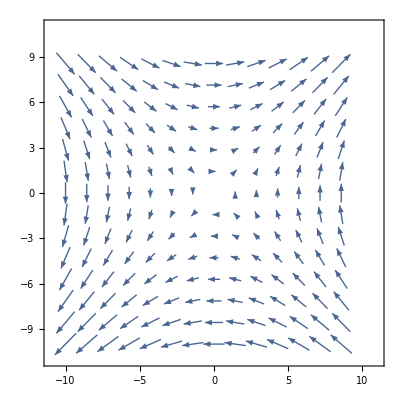

```mathematica
VectorPlot[{y,x},{x,-10,10},{y,-10,10}]
```